## Variation of Parameters-Undetermined Coefficients- Operator methods

## 1(i)

```mathematica
DSolve[y''[x]+y[x]==2 Exp[x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→ⅇ^x+C[1] Cos[x]+C[2] Sin[x]}}

{{y[x]→ⅇ^x+C[1] Cos[x]+C[2] Sin[x]}}

\left\{\left\{y(x)\to e^x+c_1 \cos (x)+c_2 \sin (x)\right\}\right\}

## 1(ii)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]-y[x]==x Exp[-2x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→1/9 ⅇ^(-2 x) (4+3 x)+ⅇ^x C[1]+ⅇ^-x C[2]}}

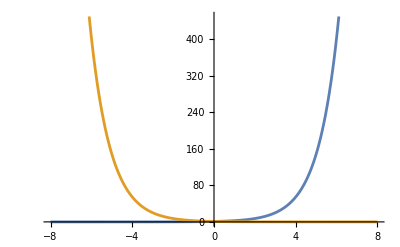

```mathematica
"plot linear components"{{y[x]->1/9 ⅇ^(-2 x) (4+3 x)+ⅇ^x C[1]+ⅇ^-x C[2]}}Plot[Evaluate[Cases[{{y[x]->1/9 ⅇ^(-2 x) (4+3 x)+ⅇ^x C[1]+ⅇ^-x C[2]}}⟦1,1,2⟧,a___ _C b___:>a b]],{x,-8,8}]
```

## 1 (iii)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+y[x]==Sin[x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]+1/4 (-2 x Cos[x]-2 Cos[x]^2 Sin[x]+Cos[x] Sin[2 x])}}

{{y[x]→(-x/2+C[1]) Cos[x]+C[2] Sin[x]}}

\left\{\left\{y(x)\to \left(-\frac{x}{2}+c_1\right) \cos (x)+c_2 \sin (x)\right\}\right\}

## 1 (iv)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+y[x]==x Sin[x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]+1/8 (-2 x^2 Cos[x]+Cos[x] Cos[2 x]-2 x Cos[2 x] Sin[x]+2 x Cos[x] Sin[2 x]+Sin[x] Sin[2 x])}}

{{y[x]→1/8 ((1-2 x^2+8 C[1]) Cos[x]+2 (x+4 C[2]) Sin[x])}}

\left\{\left\{y(x)\to \frac{1}{8} \left(\left(-2 x^2+1+8 c_1\right) \cos (x)+2 (x+4 c_2) \sin (x)\right)\right\}\right\}

## 1(v)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+y[x]==Sec[x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→C[1] Cos[x]+Cos[x] Log[Cos[x]]+x Sin[x]+C[2] Sin[x]}}

```mathematica
{{y[x]->C[1] Cos[x]+Cos[x] Log[Cos[x]]+x Sin[x]+C[2] Sin[x]}}⟦1,1,2⟧
```

C[1] Cos[x]+Cos[x] Log[Cos[x]]+x Sin[x]+C[2] Sin[x]

## 1(vi)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+y[x]==Tan[x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→-ArcTanh[Sin[x]] Cos[x]+C[1] Cos[x]+C[2] Sin[x]}}

{{y[x]→-ArcTanh[Sin[x]] Cos[x]+C[1] Cos[x]+C[2] Sin[x]}}

\left\{\left\{y(x)\to c_1 \cos (x)+c_2 \sin (x)+\cos (x) \left(-\tanh ^{-1}(\sin (x))\right)\right\}\right\}

Function[x,-ArcTanh[Sin[x]] Cos[x]+C[1] Cos[x]+C[2] Sin[x]]

## 1(vii)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+y[x]==(Sin[x])^2, y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]+1/12 (9 Cos[x]^2-Cos[x] Cos[3 x]+4 Sin[x]^4)}}

{{y[x]→1/6 (3+6 C[1] Cos[x]+Cos[2 x]+6 C[2] Sin[x])}}

\left\{\left\{y(x)\to \frac{1}{6} (\cos (2 x)+6 c_1 \cos (x)+6 c_2 \sin (x)+3)\right\}\right\}

## 1(viii)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+y[x]==Sec[x] Tan[x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→ArcTan[Tan[x]] Cos[x]+C[1] Cos[x]-Sin[x]+C[2] Sin[x]-Log[Cos[x]] Sin[x]}}

{{y[x]→ArcTan[Tan[x]] Cos[x]+C[1] Cos[x]+(-1+C[2]-Log[Cos[x]]) Sin[x]}}

\left\{\left\{y(x)\to \cos (x) \tan ^{-1}(\tan (x))+c_1 \cos (x)+\sin (x) (-\log (\cos (x))-1+c_2)\right\}\right\}

## 1(ix)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+y[x]==(Sec[x])^2, y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→-1+C[1] Cos[x]+2 ArcTanh[Tan[x/2]] Sin[x]+C[2] Sin[x]}}

{{y[x]→-1+C[1] Cos[x]+2 ArcTanh[Tan[x/2]] Sin[x]+C[2] Sin[x]}}

\left\{\left\{y(x)\to c_1 \cos (x)+c_2 \sin (x)+2 \sin (x) \tanh ^{-1}\left(\tan \left(\frac{x}{2}\right)\right)-1\right\}\right\}

{{y[x]→1/2 ⅇ^(-2 x) x^2+ⅇ^(-2 x) C[1]+ⅇ^(-2 x) x C[2]}}

{{y[x]→1/2 ⅇ^(-2 x) (x^2+2 C[1]+2 x C[2])}}

\left\{\left\{y(x)\to \frac{1}{2} e^{-2 x} \left(x^2+2 c_2 x+2 c_1\right)\right\}\right\}

{{y[x]→1/9 ⅇ^(-2 x) (4+3 x)+ⅇ^x C[1]+ⅇ^-x C[2]}}

{{y[x]→1/9 ⅇ^(-2 x) (4+3 x+9 ⅇ^(3 x) C[1]+9 ⅇ^x C[2])}}

\left\{\left\{y(x)\to \frac{1}{9} e^{-2 x} \left(3 x+9 c_1 e^{3 x}+9 c_2 e^x+4\right)\right\}\right\}

## 1(x)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+4y'[x]+4y[x]==Exp[-2x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→1/2 ⅇ^(-2 x) x^2+ⅇ^(-2 x) C[1]+ⅇ^(-2 x) x C[2]}}

{{y[x]→1/2 ⅇ^(-2 x) (x^2+2 C[1]+2 x C[2])}}

\left\{\left\{y(x)\to \frac{1}{2} e^{-2 x} \left(x^2+2 c_2 x+2 c_1\right)\right\}\right\}

## 1(xi)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+3y'[x]+2y[x]==1/(Exp[x]+1), y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→ⅇ^(-2 x) C[1]+ⅇ^-x C[2]+ⅇ^(-2 x) (-ⅇ^x+Log[1+ⅇ^x]+ⅇ^x Log[1+ⅇ^x])}}

```mathematica
Simplify[{{y[x]->ⅇ^(-2 x) C[1]+ⅇ^-x C[2]+ⅇ^(-2 x) (-ⅇ^x+Log[1+ⅇ^x]+ⅇ^x Log[1+ⅇ^x])}}]
```

{{y[x]→ⅇ^(-2 x) (C[1]+ⅇ^x (-1+C[2])+(1+ⅇ^x) Log[1+ⅇ^x])}}

## 1(xii)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+3y'[x]+2y[x]==Cos[Exp[x]], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→ⅇ^(-2 x) C[1]+ⅇ^-x C[2]-ⅇ^(-2 x) Cos[ⅇ^x]}}

{{y[x]→ⅇ^(-2 x) (C[1]+ⅇ^x C[2]-Cos[ⅇ^x])}}

\left\{\left\{y(x)\to e^{-2 x} \left(-\cos \left(e^x\right)+c_2 e^x+c_1\right)\right\}\right\}

```mathematica
Simplify[{{y[x]->ⅇ^(-2 x) C[1]+ⅇ^-x C[2]-ⅇ^(-2 x) Cos[ⅇ^x]}}]
```

{{y[x]→ⅇ^(-2 x) (C[1]+ⅇ^x C[2]-Cos[ⅇ^x])}}

## 1(xiii)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+4y'[x]+4y[x]==2Cos[2x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→ⅇ^(-2 x) C[1]+ⅇ^(-2 x) x C[2]+1/4 Sin[2 x]}}

{{y[x]→ⅇ^(-2 x) (C[1]+x C[2])+1/4 Sin[2 x]}}

\left\{\left\{y(x)\to \frac{1}{4} \sin (2 x)+e^{-2 x} (c_2 x+c_1)\right\}\right\}

## 1(xiv)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+4y'[x]+4y[x]==2Exp[-2x]Cos[2x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→ⅇ^(-2 x) C[1]+ⅇ^(-2 x) x C[2]-1/2 ⅇ^(-2 x) Cos[2 x]}}

{{y[x]→-1/2 ⅇ^(-2 x) (-2 (C[1]+x C[2])+Cos[2 x])}}

\left\{\left\{y(x)\to -\frac{1}{2} e^{-2 x} (\cos (2 x)-2 (c_2 x+c_1))\right\}\right\}

## 2(i)

```mathematica
Clear[Derivative, x]
DSolve[x^2 y''[x]+x y'[x]-y[x]==5, y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→-5+C[1]/x+x C[2]}}

{{y[x]→-5+C[1]/x+x C[2]}}

\left\{\left\{y(x)\to \frac{c_1}{x}+c_2 x-5\right\}\right\}

## 2(ii)

```mathematica
Clear[Derivative, x]
DSolve[x^2 y''[x]+x y'[x]-y[x]==2x^4, y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→(2 x^4)/15+C[1]/x+x C[2]}}

{{y[x]→(2 x^4)/15+C[1]/x+x C[2]}}

\left\{\left\{y(x)\to \frac{2 x^4}{15}+c_2 x+\frac{c_1}{x}\right\}\right\}

## 2(iii)

```mathematica
Clear[Derivative, x]
DSolve[x^2 y''[x]-x y'[x]+y[x]== x , y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→x C[1]+x C[2] Log[x]+1/2 x Log[x]^2}}

```mathematica
Simplify[{{y[x]->x C[1]+x C[2] Log[x]+1/2 x Log[x]^2}}]
```

{{y[x]→1/2 x (2 C[1]+2 C[2] Log[x]+Log[x]^2)}}

## 2(iv)

```mathematica
Clear[Derivative, x]
DSolve[x y''[x]- y'[x]== x , y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→-x^2/4+(x^2 C[1])/2+C[2]+1/2 x^2 Log[x]}}

{{y[x]→1/4 x^2 (-1+2 C[1])+C[2]+1/2 x^2 Log[x]}}

\left\{\left\{y(x)\to \frac{1}{2} x^2 \log (x)+\frac{1}{4} (-1+2 c_1) x^2+c_2\right\}\right\}

## 3(i)

```mathematica
Clear[Derivative, x]
DSolve[x^2 y''[x]+x  y'[x]-4 y[x]== x , y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→-x/3+C[1]/x^2+x^2 C[2]}}

{{y[x]→-x/3+C[1]/x^2+x^2 C[2]}}

\left\{\left\{y(x)\to c_2 x^2+\frac{c_1}{x^2}-\frac{x}{3}\right\}\right\}

## 3(ii)

```mathematica
Clear[Derivative, x]
DSolve[x^2 y''[x]+x y'[x]-4  y[x]== (1/x)+1 , y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→(-4-3 x)/(12 x)+C[1]/x^2+x^2 C[2]}}

{{y[x]→-1/4-1/(3 x)+C[1]/x^2+x^2 C[2]}}

\left\{\left\{y(x)\to c_2 x^2+\frac{c_1}{x^2}-\frac{1}{3 x}-\frac{1}{4}\right\}\right\}

## 3(iii)

```mathematica
Clear[Derivative, x]
DSolve[x^2y''[x]+x y'[x]-4  y[x]== 1/x^2, y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→C[1]/x^2+x^2 C[2]+(-1-4 Log[x])/(16 x^2)}}

{{y[x]→(-1+16 C[1]+16 x^4 C[2]-4 Log[x])/(16 x^2)}}

\left\{\left\{y(x)\to \frac{16 c_2 x^4-4 \log (x)-1+16 c_1}{16 x^2}\right\}\right\}

## 3(iv)

```mathematica
Clear[Derivative, x]
DSolve[(x-1)y''[x]-x y'[x]+  y[x]== (x-1)^2, y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→-1-x-x^2+ⅇ^x C[1]-x C[2]}}

{{y[x]→-1-x^2+ⅇ^x C[1]-x (1+C[2])}}

\left\{\left\{y(x)\to -x^2-(1+c_2) x+c_1 e^x-1\right\}\right\}

## 3 (iv)

```mathematica
Clear[Derivative, x]
DSolve[(Tan[x])^2*y''[x]-(2 Tan[x])*y'[x]+  ((Sec[x])^2+1)*y[x]== (Sin[x])^2 Tan[x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→C[1] Sin[x]+x C[2] Sin[x]-Cos[x] Sin[x]}}

{{y[x]→(C[1]+x C[2]-Cos[x]) Sin[x]}}

\{\{y(x)\to \sin (x) (-\cos (x)+c_2 x+c_1)\}\}

## 4. It follows from the relation \eqref{eq:particular-final-form} that

## 5. Use and in Problem~\ref{3-3-4}.

## 6. Follow the hint provided in the problem.

## 7. Follow the direction provided for the problem.

## 8. Find the general solution of each of the following nonhomogeneous linear differential equations.

## 8(i)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]-5y'[x]+4y[x]==5x+1, y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→1/16 (29+20 x)+ⅇ^x C[1]+ⅇ^(4 x) C[2]}}

{{y[x]→29/16+(5 x)/4+ⅇ^x C[1]+ⅇ^(4 x) C[2]}}

\left\{\left\{y(x)\to \frac{5 x}{4}+c_1 e^x+c_2 e^{4 x}+\frac{29}{16}\right\}\right\}

## 8(ii)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]-y'[x]+2y[x]==x^2+x+1, y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→1/2 (1+2 x+x^2)+ⅇ^(x/2) C[2] Cos[(√7 x)/2]+ⅇ^(x/2) C[1] Sin[(√7 x)/2]}}

{{y[x]→1/2 (1+x)^2+ⅇ^(x/2) C[2] Cos[(√7 x)/2]+ⅇ^(x/2) C[1] Sin[(√7 x)/2]}}

\left\{\left\{y(x)\to \frac{1}{2} (x+1)^2+c_2 e^{x/2} \cos \left(\frac{\sqrt{7} x}{2}\right)+c_1 e^{x/2} \sin \left(\frac{\sqrt{7} x}{2}\right)\right\}\right\}

## 8(iii)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]-5y'[x]+4y[x]==5Exp[2x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→-(5 ⅇ^(2 x))/2+ⅇ^x C[1]+ⅇ^(4 x) C[2]}}

{{y[x]→-(5 ⅇ^(2 x))/2+ⅇ^x C[1]+ⅇ^(4 x) C[2]}}

\left\{\left\{y(x)\to -\frac{5 e^{2 x}}{2}+c_1 e^x+c_2 e^{4 x}\right\}\right\}

## 8(iv)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+4y[x]==5Cos[x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→(5 Cos[x])/3+C[1] Cos[2 x]+C[2] Sin[2 x]}}

{{y[x]→(5 Cos[x])/3+C[1] Cos[2 x]+C[2] Sin[2 x]}}

\left\{\left\{y(x)\to \frac{5 \cos (x)}{3}+c_1 \cos (2 x)+c_2 \sin (2 x)\right\}\right\}

## 8(v)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+4y[x]==5Sin[2x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→C[1] Cos[2 x]+C[2] Sin[2 x]-5/16 (4 x Cos[2 x]+Cos[4 x] Sin[2 x]-Cos[2 x] Sin[4 x])}}

{{y[x]→(-(5 x)/4+C[1]) Cos[2 x]+1/8 (5+16 C[2]) Cos[x] Sin[x]}}

\left\{\left\{y(x)\to \left(-\frac{5 x}{4}+c_1\right) \cos (2 x)+\frac{1}{8} (5+16 c_2) \sin (x) \cos (x)\right\}\right\}

## 8(vi)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+4y'[x]+5y[x]==2Exp[-x]Sin[x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→ⅇ^(-2 x) C[2] Cos[x]-2/5 ⅇ^-x (2 Cos[x]-Sin[x])+ⅇ^(-2 x) C[1] Sin[x]}}

{{y[x]→1/5 ⅇ^(-2 x) ((-4 ⅇ^x+5 C[2]) Cos[x]+(2 ⅇ^x+5 C[1]) Sin[x])}}

\left\{\left\{y(x)\to \frac{1}{5} e^{-2 x} \left(\left(-4 e^x+5 c_2\right) \cos (x)+\left(2 e^x+5 c_1\right) \sin (x)\right)\right\}\right\}

## 8(vii)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+4y'[x]+4y[x]==3Exp[2x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→(3 ⅇ^(2 x))/16+ⅇ^(-2 x) C[1]+ⅇ^(-2 x) x C[2]}}

{{y[x]→(3 ⅇ^(2 x))/16+ⅇ^(-2 x) (C[1]+x C[2])}}

\left\{\left\{y(x)\to \frac{3 e^{2 x}}{16}+e^{-2 x} (c_2 x+c_1)\right\}\right\}

## 8(viii)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]-4y'[x]+4y[x]==3x Exp[2x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→1/2 ⅇ^(2 x) x^3+ⅇ^(2 x) C[1]+ⅇ^(2 x) x C[2]}}

{{y[x]→1/2 ⅇ^(2 x) (x^3+2 C[1]+2 x C[2])}}

\left\{\left\{y(x)\to \frac{1}{2} e^{2 x} \left(x^3+2 c_2 x+2 c_1\right)\right\}\right\}

## 8(ix)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]-4y'[x]+5y[x]==2Exp[2x] Sin[x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→ⅇ^(2 x) C[2] Cos[x]+ⅇ^(2 x) C[1] Sin[x]-1/2 ⅇ^(2 x) (2 x Cos[x]+Cos[2 x] Sin[x]-Cos[x] Sin[2 x])}}

{{y[x]→1/2 ⅇ^(2 x) (-2 x Cos[x]+2 C[2] Cos[x]+Sin[x]+2 C[1] Sin[x])}}

\left\{\left\{y(x)\to \frac{1}{2} e^{2 x} (\sin (x)-2 x \cos (x)+2 c_2 \cos (x)+2 c_1 \sin (x))\right\}\right\}

## 8(x)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+16y[x]==2Sin[4x]+3Cos[4x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→C[1] Cos[4 x]+C[2] Sin[4 x]+1/64 (-16 x Cos[4 x]+6 Cos[4 x]^3+24 x Sin[4 x]-4 Cos[4 x]^2 Sin[4 x]+2 Cos[4 x] Sin[8 x]+3 Sin[4 x] Sin[8 x])}}

{{y[x]→(3/32-x/4+C[1]) Cos[4 x]+1/8 (3 x+8 C[2]) Sin[4 x]}}

\left\{\left\{y(x)\to \left(-\frac{x}{4}+\frac{3}{32}+c_1\right) \cos (4 x)+\frac{1}{8} (3 x+8 c_2) \sin (4 x)\right\}\right\}

## 8(xi)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]-5y'[x]+4y[x]==5Exp[x]+3 Exp[4x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→1/9 ⅇ^x (-5-3 ⅇ^(3 x)-15 x+9 ⅇ^(3 x) x)+ⅇ^x C[1]+ⅇ^(4 x) C[2]}}

{{y[x]→1/9 ⅇ^x (-5-15 x+9 C[1]+ⅇ^(3 x) (-3+9 x+9 C[2]))}}

\left\{\left\{y(x)\to \frac{1}{9} e^x \left(-15 x+e^{3 x} (9 x-3+9 c_2)-5+9 c_1\right)\right\}\right\}

## 8(xii)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+16y[x]==x^3+1+2 Exp[4x]+ Sin[x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→C[1] Cos[4 x]+C[2] Sin[4 x]+(120 Cos[4 x]^2+120 ⅇ^(4 x) Cos[4 x]^2-45 x Cos[4 x]^2+120 x^3 Cos[4 x]^2-80 Cos[4 x] Sin[3 x]+80 Cos[3 x] Sin[4 x]-48 Cos[5 x] Sin[4 x]+120 Sin[4 x]^2+120 ⅇ^(4 x) Sin[4 x]^2-45 x Sin[4 x]^2+120 x^3 Sin[4 x]^2+48 Cos[4 x] Sin[5 x])/1920}}

{{y[x]→C[1] Cos[4 x]+Sin[x]/15+1/128 (8+8 ⅇ^(4 x)-3 x+8 x^3+128 C[2] Sin[4 x])}}

\left\{\left\{y(x)\to \frac{1}{128} \left(8 x^3-3 x+8 e^{4 x}+128 c_2 \sin (4 x)+8\right)+\frac{\sin (x)}{15}+c_1 \cos (4 x)\right\}\right\}

## 8(xiii)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]-y'[x]==1+7 Exp[x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→-x+ⅇ^x (-7+7 x+C[1])+C[2]}}

{{y[x]→-x+ⅇ^x (-7+7 x+C[1])+C[2]}}

\left\{\left\{y(x)\to -x+e^x (7 x-7+c_1)+c_2\right\}\right\}

## 8(xiv)

```mathematica
Clear[Derivative, x]
DSolve[y''[x]+y'[x]==2+Sin[x]-7 Exp[-x], y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→C[2]+1/2 (4 x+2 ⅇ^-x (7+7 x-C[1])-Cos[x]-Sin[x])}}

{{y[x]→2 x+ⅇ^-x (7+7 x-C[1])+C[2]-Cos[x]/2-Sin[x]/2}}

\left\{\left\{y(x)\to 2 x-\frac{\sin (x)}{2}-\frac{\cos (x)}{2}+e^{-x} (7 x+7-c_1)+c_2\right\}\right\}

## 9(i)

```mathematica
Clear[Derivative, x]
ode:=y''[x]+ω^2* y[x]== 5 Cos[γ* x]
ics:={y[0]==0, y'[0]==0}
DSolve[{ode, ics}, y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→-(5 (Cos[x γ]-Cos[x ω]))/(γ^2-ω^2)}}

{{y[x]→-(5 (Cos[x γ]-Cos[x ω]))/(γ^2-ω^2)}}

\left\{\left\{y(x)\to -\frac{5 (\cos (\gamma  x)-\cos (x \omega ))}{\gamma ^2-\omega ^2}\right\}\right\}

## 9(ii)

```mathematica
ClearAll
Limit[-(5 (Cos[x γ]-Cos[x ω]))/(γ^2-ω^2),γ-> ω]
Simplify[%]
TeXForm[%]
```

ClearAll

(5 x Sin[x ω])/(2 ω)

(5 x Sin[x ω])/(2 ω)

\frac{5 x \sin (x \omega )}{2 \omega }

## 9(iii) Routine check

## 9 (iv)

```mathematica
Clear[Derivative, x]
ode:=y''[x]+ω^2* y[x]== 5 Cos[ω* x]
ics:={y[0]==0, y'[0]==0}
DSolve[{ode,ics}, y[x], x]
Simplify[%]
DSolve[ode, y[x], x]
Simplify[%]
TeXForm[%]
```

{{y[x]→(5 (-Cos[x ω]+Cos[x ω] Cos[2 x ω]+2 x ω Sin[x ω]+Sin[x ω] Sin[2 x ω]))/(4 ω^2)}}

{{y[x]→(5 x Sin[x ω])/(2 ω)}}

{{y[x]→C[1] Cos[x ω]+C[2] Sin[x ω]+(5 (Cos[x ω] Cos[2 x ω]+2 x ω Sin[x ω]+Sin[x ω] Sin[2 x ω]))/(4 ω^2)}}

{{y[x]→((5+4 ω^2 C[1]) Cos[x ω]+2 ω (5 x+2 ω C[2]) Sin[x ω])/(4 ω^2)}}

\left\{\left\{y(x)\to \frac{\left(5+4 c_1 \omega ^2\right) \cos (x \omega )+2 \omega  (5 x+2 c_2 \omega ) \sin (x \omega )}{4 \omega ^2}\right\}\right\}

## 10(i), (ii)

```mathematica
Clear[Derivative, x]
ode:=y''[x]+ y[x]==10Sin[2x]
ics:={y[0]==0, y'[0]==0}
sol1=DSolve[{ode,ics}, y[x], x]
solu1=y[x]/.sol1[[1]];
Simplify[%]
(*DSolve[ode, y[x], x]*)
(*Simplify[%]*)
TeXForm[%]
```

{{y[x]→10/3 (2 Sin[x]-Sin[2 x])}}

10/3 (2 Sin[x]-Sin[2 x])

\frac{10}{3} (2 \sin (x)-\sin (2 x))

```mathematica
Clear[Derivative, x]
ode:=y''[x]+ y[x]== 10Sin[ x]
ics:={y[0]==0, y'[0]==0}
sol2=DSolve[{ode,ics}, y[x], x]
solu2=y[x]/.sol2[[1]];
Simplify[%]
(*DSolve[ode, y[x], x]*)
(*Simplify[%]*)
TeXForm[%]
```

{{y[x]→-5/2 (2 x Cos[x]-Sin[x]+Cos[2 x] Sin[x]-Cos[x] Sin[2 x])}}

-5 x Cos[x]+5 Sin[x]

5 \sin (x)-5 x \cos (x)

```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath,amssymb,amsfonts}","\\usepackage{lmodern}"}];
SetDirectory[NotebookDirectory[]]
textStyle={FontFamily->"LM Roman 12",FontSize->30};
```

/Users/dadhikar/Library/CloudStorage/OneDrive-KennesawStateUniversity(2)/MyBooks/A_ODE_Project/chap03/mathematica

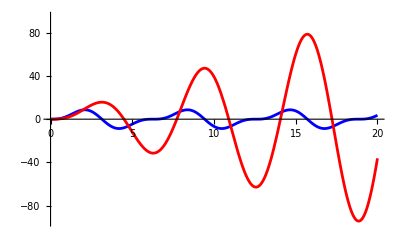

```mathematica
plot1=Plot[{solu1,solu2},{x,0,20},PlotLegends->Placed[SwatchLegend[MaTeX[{"y=\\frac{10}{3} (2 \\sin (x)-\\sin (2 x))","y=5 \\sin (x)-5 x \\cos (x)"},Magnification->1.8]],Bottom],PlotStyle->{Blue,Red},PlotRange->{{0,20},{-95,95}},
AxesLabel->{MaTeX["x",Magnification->2],MaTeX["",Magnification->2]}, AxesStyle->Directive[FontSize->20,FontFamily->"LM Roman 12"],
LabelStyle->Directive[FontSize->12,FontFamily->"LM Roman 12"]]
```

```mathematica
Export["3-3-10a.pdf",plot1]
```

3-3-10a.pdf

## 11

```mathematica
Clear[Derivative, x]
ode:=y''[x]-9 y[x]== Exp[3 x]
(*ics:={y[0]==0, y'[0]==0}*)
sol2=DSolve[ode, y[x], x]
solu2=y[x]/.sol2[[1]];
Expand[%]
(*DSolve[ode, y[x], x]*)
(*Simplify[%]*)
TeXForm[%]
```

{{y[x]→1/36 ⅇ^(3 x) (-1+6 x)+ⅇ^(3 x) C[1]+ⅇ^(-3 x) C[2]}}

-ⅇ^(3 x)/36+1/6 ⅇ^(3 x) x+ⅇ^(3 x) C[1]+ⅇ^(-3 x) C[2]

\frac{1}{6} e^{3 x} x-\frac{e^{3 x}}{36}+c_1 e^{3 x}+c_2 e^{-3 x}

## 12

```mathematica
Clear[Derivative, x]
ode:=y''[x]-9 y[x]== Exp[-3 x]
(*ics:={y[0]==0, y'[0]==0}*)
sol2=DSolve[ode, y[x], x]
solu2=y[x]/.sol2[[1]];
Expand[%]
(*DSolve[ode, y[x], x]*)
(*Simplify[%]*)
TeXForm[%]
```

{{y[x]→-1/36 ⅇ^(-3 x) (1+6 x)+ⅇ^(3 x) C[1]+ⅇ^(-3 x) C[2]}}

-1/36 ⅇ^(-3 x)-1/6 ⅇ^(-3 x) x+ⅇ^(3 x) C[1]+ⅇ^(-3 x) C[2]

-\frac{1}{6} e^{-3 x} x-\frac{e^{-3 x}}{36}+c_1 e^{3 x}+c_2 e^{-3 x}

## 13(i)

```mathematica
Clear[Derivative, x]
ode:=y''[x]-6y'[x]+9 y[x]==x  Exp[3 x]
(*ics:={y[0]==0, y'[0]==0}*)
sol2=DSolve[ode, y[x], x]
solu2=y[x]/.sol2[[1]];
Expand[%]
(*DSolve[ode, y[x], x]*)
(*Simplify[%]*)
TeXForm[%]
```

{{y[x]→1/6 ⅇ^(3 x) x^3+ⅇ^(3 x) C[1]+ⅇ^(3 x) x C[2]}}

1/6 ⅇ^(3 x) x^3+ⅇ^(3 x) C[1]+ⅇ^(3 x) x C[2]

\frac{1}{6} e^{3 x} x^3+c_2 e^{3 x} x+c_1 e^{3 x}

## 13(ii)

```mathematica
Clear[Derivative, x]
ode:=y''[x]-2y'[x]-3 y[x]==16 Exp[5 x]
(*ics:={y[0]==0, y'[0]==0}*)
sol2=DSolve[ode, y[x], x]
solu2=y[x]/.sol2[[1]];
Expand[%]
(*DSolve[ode, y[x], x]*)
(*Simplify[%]*)
TeXForm[%]
```

{{y[x]→(4 ⅇ^(5 x))/3+ⅇ^-x C[1]+ⅇ^(3 x) C[2]}}

(4 ⅇ^(5 x))/3+ⅇ^-x C[1]+ⅇ^(3 x) C[2]

\frac{4 e^{5 x}}{3}+c_1 e^{-x}+c_2 e^{3 x}

## 14

## Follow the directions provided

## 15(i)

```mathematica
Clear[Derivative, x]
ode:=y''[x]+(x+1)y'[x]+(x+1) y[x]==Exp[-x]
(*ics:={y[0]==0, y'[0]==0}*)
sol2=DSolve[ode, y[x], x]
solu2=y[x]/.sol2[[1]];
Simplify[%]
(*DSolve[ode, y[x], x]*)
(*Simplify[%]*)
TeXForm[%]
```

{{y[x]→ⅇ^(-x^2/2) C[1]+ⅇ^(-1/2-x^2/2) √(π/2) C[2] Erfi[(-1+x)/(√2)]+1/2 ⅇ^(-1/2-x^2/2) √π ((2 ⅇ^(1/2 (-1+x)^2))/(√π)+√2 Erfi[(-1+x)/(√2)])}}

1/2 ⅇ^(1/2 (-1-x^2)) (2 (ⅇ^(1/2 (-1+x)^2)+√ⅇ C[1])+√(2 π) (1+C[2]) Erfi[(-1+x)/(√2)])

\frac{1}{2} e^{\frac{1}{2} \left(-x^2-1\right)} \left(\sqrt{2 \pi } (1+c_2) \text{erfi}\left(\frac{x-1}{\sqrt{2}}\right)+2 \left(e^{\frac{1}{2} (x-1)^2}+\sqrt{e} c_1\right)\right)

```mathematica
Simplify[1/2 ⅇ^(-1/2-x^2/2) √π ((2 ⅇ^(1/2 (-1+x)^2))/(√π))]
```

ⅇ^-x

## 16

```mathematica
Clear[Derivative, x]
ode:=y''[x]+(x+1)y'[x]+x y[x]==0
(*ics:={y[0]==0, y'[0]==0}*)
sol2=DSolve[ode, y[x], x]
solu2=y[x]/.sol2[[1]];
Simplify[%]
(*DSolve[ode, y[x], x]*)
(*Simplify[%]*)
TeXForm[%]
```

{{y[x]→ⅇ^(-x^2/2+(-1/(√2)+x/(√2))^2) C[2]+ⅇ^(-x^2/2) C[1] HermiteH[-1,-1/(√2)+x/(√2)]}}

ⅇ^(-x^2/2) (ⅇ^(1/2 (-1+x)^2) C[2]+C[1] HermiteH[-1,(-1+x)/(√2)])

e^{-\frac{x^2}{2}} \left(c_1 H_{-1}\left(\frac{x-1}{\sqrt{2}}\right)+c_2 e^{\frac{1}{2} (x-1)^2}\right)